showing stability of P4 at the chosen values of sigma.

```mathematica
xdot=w*x*(1-x)-δ1(1-w)x;
ydot=μ*w*x^2(1-y)-η*y-δ2(1-w)y;
zdot=γ*w*z*(1-z)-δ3(1-w)*z;
wdot=ρ(1-w)w-σ*w;
```

```mathematica
xbar=(ρ-σ-δ1*σ)/(ρ-σ);
ybar=(μ(ρ-σ-δ1*σ)^2)/(μ(ρ-σ-δ1*σ)^2+(ρ-σ)(η*ρ+δ2*σ));
zbar=(γ*ρ-γ*σ-δ3*σ)/(γ(ρ-σ));
wbar=(ρ-σ)/ρ;
```

```mathematica
jacobian=D[{xdot,ydot,zdot,wdot},{{x,y,z,w}}]
```

{{w (1-x)-w x-(1-w) δ1,0,0,(1-x) x+x δ1},{2 w x (1-y) μ,-(1-w) δ2-η-w x^2 μ,0,y δ2+x^2 (1-y) μ},{0,0,w (1-z) γ-w z γ-(1-w) δ3,(1-z) z γ+z δ3},{0,0,0,(1-w) ρ-w ρ-σ}}

```mathematica
curestate=jacobian/.{x->0,y->0,z->zbar,w->wbar}
```

{{-δ1 (1-(ρ-σ)/ρ)+(ρ-σ)/ρ,0,0,0},{0,-η-δ2 (1-(ρ-σ)/ρ),0,0},{0,0,-δ3 (1-(ρ-σ)/ρ)-(γ ρ-γ σ-δ3 σ)/ρ+(γ (ρ-σ) (1-(γ ρ-γ σ-δ3 σ)/(γ (ρ-σ))))/ρ,(δ3 (γ ρ-γ σ-δ3 σ))/(γ (ρ-σ))+((γ ρ-γ σ-δ3 σ) (1-(γ ρ-γ σ-δ3 σ)/(γ (ρ-σ))))/(ρ-σ)},{0,0,0,-ρ+ρ (1-(ρ-σ)/ρ)}}

```mathematica
FullSimplify[curestate/.replacement]
```

{{1.-3.875 σ,0,0,0},{0,-0.25-1.625 σ,0,0},{0,0,-0.75+2.375 σ,(0.032+(-0.101333+5.55112×10^-17 σ) σ)/(-0.4+σ)^2},{0,0,0,-0.4+1. σ}}

```mathematica
eigs=Eigenvalues[curestate]
```

{-ρ+σ,(ρ-σ-δ1 σ)/ρ,-(η ρ+δ2 σ)/ρ,-(γ ρ-γ σ-δ3 σ)/ρ}

```mathematica
replacement={ρ->0.40,γ->0.75,δ3->0.20,δ1->0.55,μ->0.50,η->0.25,δ2->0.65}
```

{ρ→0.4,γ→0.75,δ3→0.2,δ1→0.55,μ→0.5,η→0.25,δ2→0.65}

```mathematica
eigvalues=FullSimplify[eigs/.replacement]
```

{-0.4+σ,1.-3.875 σ,-0.25-1.625 σ,-0.75+2.375 σ}

```mathematica
eigens=Plot[{-0.4+σ,1-3.875* σ,-0.25-1.625σ,-0.75+2.375σ},{σ,0,0.4},PlotLegends->Placed[{Style["λ1",36],Style["λ2",36],Style["λ3",36],Style["λ4",36]},{Bottom,Bottom}],TicksStyle->32,AxesStyle->Directive[Large,Thick],PlotStyle->Directive[Thickness[0.005]]]
```

-Graphics-

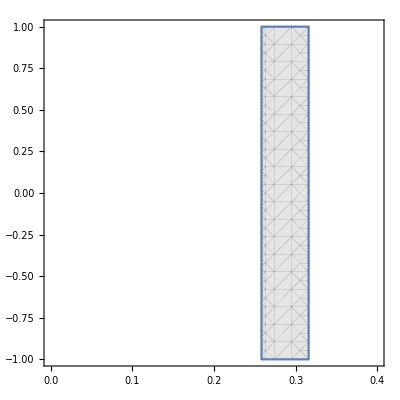

```mathematica
area=RegionPlot[0.4/1.55<σ<0.4/(1+0.2/0.75),{σ,0,0.4},{y,-1,1},PlotStyle->{Opacity[0.2],Gray}]
```

```mathematica
Show[eigens,area,ImageSize->Full]
```

-Graphics-

```mathematica
0.4/0.155
```

2.58065

```mathematica
0.4/(1+0.2/0.75)
```

0.315789